```mathematica
Abs'[x_]:=Sign[x]
```

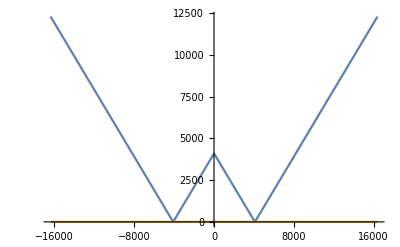

```mathematica
L:=8192 (*length of buffer*)
W:=4    (*some position for write pointer*)
foo[r_]:=Abs[Abs[W-r]-L/2] (* function to minimize *)
zz[s_]:=foo[s-foo'[s]*foo[s]] (* result of minimization applied to s. To minimize, we pushed s in the opposite direction of the derivative*)
(*foo[s] happens to also give the magnitude of gradient needed to make foo[s - gradient] == 0*)
Plot[{foo[r],zz[r]}, {r,-2L,2L}]
```